Iteration: 1

Fitness of height constraint: 21.5479

Fitness of angle constraint: 7.0509

Overall Fitness: 0.188234(5.31254)

R1 = 1.9; R2 = 1; R2prime = 1; R3 = 4.65; R3prime = 2.3; R4 = 2.35; R5 = 3.65; R6 = 4.65;

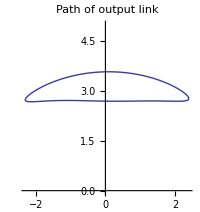
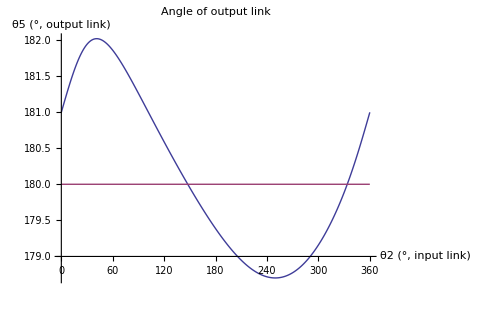

Iteration: 77

Fitness of height constraint: 18.9944

Fitness of angle constraint: 7.42739

Overall Fitness: 0.187284(5.33948)

R1 = 1.9; R2 = 1; R2prime = 1; R3 = 4.65; R3prime = 2.4; R4 = 2.4; R5 = 3.65; R6 = 4.65;

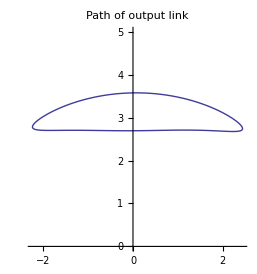
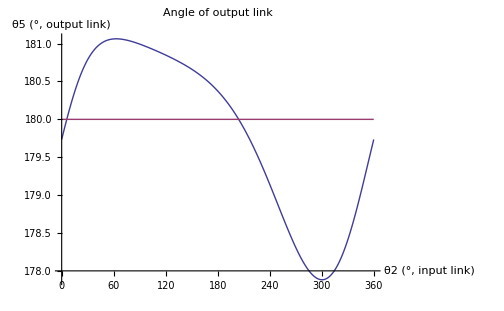

```mathematica
R1=1.333;
R2=0.8;
R2prime=0.8;
R3=3.7;
R3prime=1.7;
R4=1.8;
R5=2.75;
R5prime=1.75;
R6=3.666;
RP=1;

(* New Values*)
(*R1 = 1.4997; R2 = 0.8; R2prime = 0.8; R3 = 3.63227; R3prime = 1.8653; R4 = 1.88335; R5 = 2.8632; R5prime = 1.75; R6 = 3.6639;*)
(*R1 = 1.50994; R2 = 0.8; R2prime = 0.8; R3 = 3.73976; R3prime = 1.87298; R4 = 1.87472; R5 = 3.0179; R6 = 3.74617;*)
(*R1 = 1.5; R2 = 0.8; R2prime = 0.8; R3 = 3.75; R3prime = 1.85; R4 = 1.85; R5 = 3.05; R6 = 3.75; BEST!*)
R1 = 1.9; R2 = 1; R2prime = 1; R3 = 4.65; R3prime = 2.3; R4 = 2.35; R5 = 3.65; R6 = 4.65;

fitnessBest=1000;
n=1;While[n<1000000,
{ℛ1=R1 ⅇ^(ⅈ 0);
ℛ2=R2 ⅇ^(ⅈ θR2);
ℛ2prime=R2prime ⅇ^(ⅈ (θR2+180°));
ℛ3=R3 ⅇ^(ⅈ θR3);
ℛ3prime=R3prime ⅇ^(ⅈ θR3);
ℛ4=R4 ⅇ^(ⅈ θR4);
ℛ5=R5 ⅇ^(ⅈ θR5);
ℛ5prime=R5prime ⅇ^(ⅈ θR5);
ℛP=0;
ℛ6=R6 ⅇ^(ⅈ θR6);
ℛP=RP ⅇ^(ⅈ (θR5+90°));
θ5=Table[
{1,θR5/.FindRoot[
{
Re[ℛ2+ℛ3prime]==Re[ℛ1+ℛ4],
Im[ℛ2+ℛ3prime]==Im[ℛ1+ℛ4],
Re[ℛ2+ℛ3+ℛ5]==Re[ℛ2prime+ℛ6],
Im[ℛ2+ℛ3+ℛ5]==Im[ℛ2prime+ℛ6]
},
{{ θR3,45°},{ θR4,100°},{ θR5,180°},{ θR6,90°}}
]
},{θR2,0°,360°,1°}]//Quiet;
dy=Table[
{2.70-Im[(ℛ2+ℛ3+ℛ5prime+ℛP)/.FindRoot[
{
Re[ℛ2+ℛ3prime]==Re[ℛ1+ℛ4],
Im[ℛ2+ℛ3prime]==Im[ℛ1+ℛ4],
Re[ℛ2+ℛ3+ℛ5]==Re[ℛ2prime+ℛ6],
Im[ℛ2+ℛ3+ℛ5]==Im[ℛ2prime+ℛ6]
},
{{ θR3,45°},{ θR4,100°},{ θR5,180°},{ θR6,90°}}
]
]},{θR2,80°,300°,1°}]//Quiet;
imax=Length[dy[[All]]];
fitnessdy=2∑_i^imax (dy[[i]][[1]])^2;
imax=Length[θ5[[All,2]]];
fitnessθ5=∑_i^imax (π-θ5[[All,2]][[i]])^2;
totalFitness=fitnessdy+fitnessθ5;
If[totalFitness<fitnessBest,
{
fitnessBest=totalFitness;
Print["Iteration: ",n];
Print["Fitness of height constraint: ",(1/fitnessdy)];
Print["Fitness of angle constraint: ",(1/fitnessθ5)];
Print["Overall Fitness: ",totalFitness, "(",(1/totalFitness),")"];
Print["R1 = "<>ToString[R1]<>"; R2 = "<>ToString[R2]<>"; R2prime = "<>ToString[R2prime]<>"; R3 = "<>ToString[R3]<>"; R3prime = "<>ToString[R3prime]<>"; R4 = "<>ToString[R4]<>"; R5 = "<>ToString[R5]<>"; R6 = "<>ToString[R6]<>";"];

LinkPath=Table[
{Re[(ℛ2+ℛ3+ℛ5prime+ℛP)/.(θs=FindRoot[
{
Re[ℛ2+ℛ3prime]==Re[ℛ1+ℛ4],
Im[ℛ2+ℛ3prime]==Im[ℛ1+ℛ4],
Re[ℛ2+ℛ3+ℛ5]==Re[ℛ2prime+ℛ6],
Im[ℛ2+ℛ3+ℛ5]==Im[ℛ2prime+ℛ6]
},
{{ θR3,45°},{ θR4,100°},{ θR5,180°},{ θR6,90°}}
])],
Im[(ℛ2+ℛ3+ℛ5prime+ℛP)/.θs]
},{θR2,0°,360°,1°}]//Quiet;

θ5=Table[{θR2,θR5/.FindRoot[
{
Re[ℛ2+ℛ3prime]==Re[ℛ1+ℛ4],
Im[ℛ2+ℛ3prime]==Im[ℛ1+ℛ4],
Re[ℛ2+ℛ3+ℛ5]==Re[ℛ2prime+ℛ6],
Im[ℛ2+ℛ3+ℛ5]==Im[ℛ2prime+ℛ6]
},
{{ θR3,45°},{ θR4,100°},{ θR5,180°},{ θR6,90°}}
]},{θR2,0°,360°,1°}]//Quiet;

Print[ListLinePlot[LinkPath,AspectRatio-> Automatic,PlotRange->5,ImageSize->200,PlotLabel->"Path of output link"],ListLinePlot[{θ5/°,{{0,π/°},{2π/°,π/°}}},ImageSize->500,AxesLabel->{"θ2 (°, input link)","θ5 (°, output link)"},PlotLabel->"Angle of output link"]];
R1Last=R1;
(*R2Last=R2;*)
(*R2PLast=R2P;*)
R3Last=R3;
R3PLast=R3prime;
R4Last=R4;
R5Last=R5;
R6Last=R6;
(**)
R1+=((Random[]-0.5)*5//Floor)*0.05;
(*R2+=(Random[]-.5)/2;*)
(*R2prime+=(Random[]-.5)/2;*)
R3+=((Random[]-0.5)*5//Floor)*0.05;
R3prime+=((Random[]-0.5)*5//Floor)*0.05;
R4+=((Random[]-0.5)*5//Floor)*0.05;
R5+=((Random[]-0.5)*5//Floor)*0.05;
R6+=((Random[]-0.5)*5//Floor)*0.05;
},
{
R1=R1Last;
(*R2=R2Last;*)
(*R2P=R2PLast;*)
R3=R3Last;
R3prime=R3PLast;
R4=R4Last;
R5=R5Last;
R6=R6Last;
(**)
R1+=((Random[]-0.5)*5//Floor)*0.05;
(*R2+=(Random[]-.5)/2;*)
(*R2prime+=(Random[]-.5)/2;*)
R3+=((Random[]-0.5)*5//Floor)*0.05;
R3prime+=((Random[]-0.5)*5//Floor)*0.05;
R4+=((Random[]-0.5)*5//Floor)*0.05;
R5+=((Random[]-0.5)*5//Floor)*0.05;
R6+=((Random[]-0.5)*5//Floor)*0.05;
}]
n++;
}]
```